```mathematica
resSingle = {0.00141909889,0.00163355654,0.00128639145,0.0013485876,0.00225878445,0.00190157436,0.00157771355,0.00248723336,0.000826638135,0.00173904442,0.00169189594,0.00157105544,0.00234504695,0.00158675562,0.00125118125,0.00201556658,0.00174497648,0.00209157264,0.00269306045,0.0035581623,0.00401827015,0.00266757721,0.000427825449,0.00383004222,0.0046370656,0.0036754669,0.0041714714,0.000160239734,0.00469606326,0.00448687522,0.00547558406,0.00505925936,0.00460513218,0.00253942508,0.00479151801,0.00388057373,0.00489416601,0.00414269645,107.761695}
```

{0.0014191,0.00163356,0.00128639,0.00134859,0.00225878,0.00190157,0.00157771,0.00248723,0.000826638,0.00173904,0.0016919,0.00157106,0.00234505,0.00158676,0.00125118,0.00201557,0.00174498,0.00209157,0.00269306,0.00355816,0.00401827,0.00266758,0.000427825,0.00383004,0.00463707,0.00367547,0.00417147,0.00016024,0.00469606,0.00448688,0.00547558,0.00505926,0.00460513,0.00253943,0.00479152,0.00388057,0.00489417,0.0041427,107.762}

```mathematica
resAll = {0.00145756486,0.00180727905,0.00186536342,0.00161298296,0.00194717866,0.00170580009,0.00167423386,0.0023152398,0.00173683272,0.00196466475,0.00174678502,0.00175203665,0.00189861553,0.00192549761,0.00160604398,0.00185130817,0.00180849818,0.0021214869,0.00268619142,0.00235996959,0.00342621318,0.0035423356,0.00225109243,0.0031020052,0.00271860563,0.00262167771,0.0037924023,0.0035986003,0.00395571965,0.00279145592,0.00358232934,0.00443149452,0.0039928514,0.00211168309,0.00380296933,0.00292979399,0.00257933143,0.00460506687,108.399686}
```

{0.00145756,0.00180728,0.00186536,0.00161298,0.00194718,0.0017058,0.00167423,0.00231524,0.00173683,0.00196466,0.00174679,0.00175204,0.00189862,0.0019255,0.00160604,0.00185131,0.0018085,0.00212149,0.00268619,0.00235997,0.00342621,0.00354234,0.00225109,0.00310201,0.00271861,0.00262168,0.0037924,0.0035986,0.00395572,0.00279146,0.00358233,0.00443149,0.00399285,0.00211168,0.00380297,0.00292979,0.00257933,0.00460507,108.4}

```mathematica
resSingle[[1;;1 + 19-1]]
resSingle[[20;;20+19-1]]
```

{0.0014191,0.00163356,0.00128639,0.00134859,0.00225878,0.00190157,0.00157771,0.00248723,0.000826638,0.00173904,0.0016919,0.00157106,0.00234505,0.00158676,0.00125118,0.00201557,0.00174498,0.00209157,0.00269306}

{0.00355816,0.00401827,0.00266758,0.000427825,0.00383004,0.00463707,0.00367547,0.00417147,0.00016024,0.00469606,0.00448688,0.00547558,0.00505926,0.00460513,0.00253943,0.00479152,0.00388057,0.00489417,0.0041427}

```mathematica
resAll[[1;;1 + 19-1]]
resAll[[20;;20+19-1]]
```

{0.00145756,0.00180728,0.00186536,0.00161298,0.00194718,0.0017058,0.00167423,0.00231524,0.00173683,0.00196466,0.00174679,0.00175204,0.00189862,0.0019255,0.00160604,0.00185131,0.0018085,0.00212149,0.00268619}

{0.00235997,0.00342621,0.00354234,0.00225109,0.00310201,0.00271861,0.00262168,0.0037924,0.0035986,0.00395572,0.00279146,0.00358233,0.00443149,0.00399285,0.00211168,0.00380297,0.00292979,0.00257933,0.00460507}

```mathematica
myGreen = CMYKColor[1.0,0,.16,.31]
myPink = CMYKColor[.0,1.0,0.14,.17]
```

RGBColor[0, 156, 88]

CMYKColor[1., 0, 0.16, 0.31]

CMYKColor[0., 1., 0.14, 0.17]

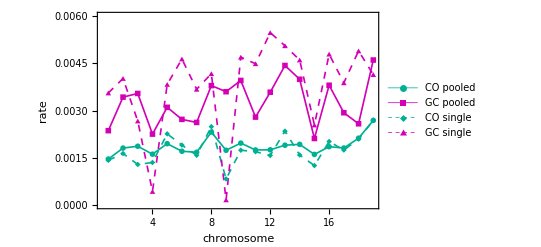

/home/derek/Dropbox/projects/gene_conversion/mouse_bootstrap_results/mouseSingleVsPooledEstimates.svg

```mathematica
pltSingleVsPoolEstimates = ListPlot[{
resAll[[1;;1 + 19-1]],
resAll[[20;;20+19-1]],
resSingle[[1;;1 + 19-1]],
resSingle[[20;;20+19-1]]},
PlotRange->{All,{0,0.006}},Joined->True,
PlotStyle->{{Thickness[0.003],myGreen},{Thickness[0.003],myPink},{Thickness[0.003],Dashed,myGreen},{Thickness[0.003],Dashed,myPink}},PlotMarkers->{Automatic,Scaled[0.03]},
PlotStyle->{{myGreen},{myPink},{Dotted,myGreen},{Dotted,myPink}},PlotMarkers->Automatic,PlotLegends->{"CO pooled","GC pooled", "CO single","GC single"},

Frame->True,FrameStyle->Directive[12,Bold,Thick,Darker@Gray],FrameLabel->{"chromosome","rate"},
ImageSize->Automatic
]
```

```mathematica
resAllSinlgeRho = {0.0024282,0.00330779,0.00340688,0.00255148,0.00330316,0.00285753,0.00278443,0.00404483,0.00329535,0.00371671,0.00294055,0.00332221,0.00386993,0.0036916,0.00247676,0.00353591,0.00306366,0.00324592,0.00486269}
```

{0.0024282,0.00330779,0.00340688,0.00255148,0.00330316,0.00285753,0.00278443,0.00404483,0.00329535,0.00371671,0.00294055,0.00332221,0.00386993,0.0036916,0.00247676,0.00353591,0.00306366,0.00324592,0.00486269}

```mathematica
simSingleRho={0.0026337,0.00359571,0.00357564,0.00261904,0.00338541,0.00297479,0.0030067,0.00420282,0.00336432,0.00395792,0.00301397,0.00316711,0.00415027,0.00365367,0.00252353,0.00361901,0.0031269,0.00354406,0.00507593};
```

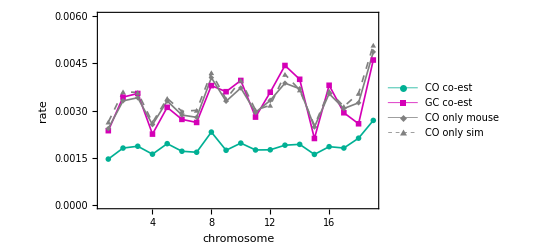

```mathematica
pltWithVsWithoutGCModel = ListPlot[{
resAll[[1;;1 + 19-1]],
resAll[[20;;20+19-1]],
resAllSinlgeRho,
simSingleRho},
PlotRange->{All,{0,0.006}},Joined->True,
PlotStyle->{{Thickness[0.003],myGreen},{Thickness[0.003],myPink},{Thickness[0.003],Normal[Gray]},{Thickness[0.003],Dashed,Normal[Gray]}},PlotMarkers->{Automatic,Scaled[0.03]},PlotLegends->{"CO co-est","GC co-est","CO only mouse","CO only sim"},
Frame->True,FrameStyle->Directive[12,Bold,Thick,Darker@Gray],FrameLabel->{"chromosome","rate"},
ImageSize->Automatic
]
```